# Test and Filter Runs

n: number of stars
NS: number of simulations
R: virial radius
Isolated System

### Logs

```mathematica
Print[$RunNumber]
```

250

```mathematica
Print[script`path]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest

```mathematica
logstream = OpenWrite[
FileNameJoin[{script`path, "nbstatus" <> ToString[$RunNumber] <> ".log"}],
FormatType->OutputForm
]
```

OutputStream[…]

```mathematica
Write[logstream, "Begin log ...."];
```

## Initialization

```mathematica
{$MachineName,$Version}
```

{tars,12.1.0 for Linux x86 (64-bit) (March 18, 2020)}

```mathematica
AppendTo[$Path,Environment["MYGITDIR"]];
```

```mathematica
Get["AstroTools`nbody6`"]
```

```mathematica
Get["AstroTools`Utilities`"]
```

```mathematica
$ConfiguredKernels = 
 List[SubKernels`LocalKernels`LocalMachine[30, 
   Rule[SubKernels`LocalKernels`LowerPriority, True]]]
```

{SubKernels`LocalKernels`LocalMachine[30,SubKernels`LocalKernels`LowerPriority→True]}

```mathematica
resultsPath=FileNameJoin[{Environment["MYGITDIR"],"workspace","nbody6","isolated","n"<>ToString[$RunNumber],"NSX-R1","results"}]
```

/home/cesarg/git/workspace/nbody6/isolated/n250/NSX-R1/results

```mathematica
SetDirectory[resultsPath]
```

/home/cesarg/git/workspace/nbody6/isolated/n250/NSX-R1/results

```mathematica
FileNames[]
```

{goodRuns.log,run-1,run-100,run-101,run-106,run-110,run-111,run-113,run-120,run-121,run-122,run-124,run-131,run-132,run-135,run-136,run-140,run-146,run-149,run-152,run-153,run-154,run-156,run-157,run-158,run-16,run-160,run-161,run-163,run-165,run-169,run-173,run-181,run-189,run-198,run-203,run-209,run-213,run-219,run-229,run-232,run-233,run-239,run-24,run-243,run-246,run-252,run-253,run-256,run-259,run-264,run-265,run-268,run-272,run-275,run-277,run-280,run-283,run-284,run-288,run-289,run-290,run-292,run-298,run-302,run-306,run-310,run-312,run-314,run-318,run-329,run-331,run-333,run-334,run-337,run-339,run-34,run-347,run-349,run-350,run-351,run-354,run-357,run-358,run-361,run-365,run-366,run-370,run-372,run-374,run-38,run-383,run-384,run-385,run-390,run-396,run-4,run-400,run-404,run-405,run-407,run-409,run-412,run-416,run-418,run-419,run-420,run-423,run-428,run-44,run-441,run-442,run-444,run-450,run-453,run-454,run-456,run-460,run-464,run-465,run-467,run-468,run-47,run-472,run-474,run-475,run-478,run-480,run-485,run-486,run-488,run-49,run-491,run-497,run-499,run-50,run-501,run-503,run-506,run-512,run-513,run-518,run-519,run-522,run-528,run-530,run-537,run-541,run-551,run-555,run-559,run-563,run-564,run-565,run-568,run-569,run-574,run-576,run-579,run-580,run-584,run-592,run-593,run-6,run-603,run-606,run-607,run-61,run-614,run-621,run-623,run-627,run-63,run-630,run-635,run-639,run-645,run-655,run-656,run-658,run-66,run-661,run-669,run-67,run-68,run-680,run-683,run-69,run-690,run-693,run-694,run-695,run-697,run-698,run-703,run-707,run-71,run-711,run-712,run-713,run-716,run-717,run-719,run-72,run-722,run-724,run-725,run-728,run-731,run-732,run-733,run-737,run-738,run-739,run-742,run-76,run-77,run-8,run-82,run-88,run-89,run-91,run-93,run-94,run-99}

### n–body parameters

```mathematica
(*
numberOfStars=380;
nb["S0"]=0.3(numberOfStars/1000)^(1/3)
nb["nMAX"]=2.(numberOfStars)^(1/2)
*)
```

```mathematica
FilePrint["../create-ini.sh"]
```

#!/bin/bash
# first group 1-250

echo "[`date`] Start"

cd results/
for filenumber in {1..750..1}
do
	mkdir "./run-$filenumber/"
  	cat << EOF > ./run-$filenumber/ini.dat
1 20.0
250 1 10 $RANDOM 35 1
0.01 0.01 0.2 1.0 1.0 900.0 1.0E-03 1 0.5
0 0 1 0 1 0 0 0 0 0
0 0 0 0 0 0 0 0 0 6
0 0 0 0 0 0 0 0 0 0
0 0 0 0 0 0 0 0 0 1
0 0 0 0 0 0 0 0 0 0
4.0E-05 0.001 0.2 1.0 1.0E-06 0.001
2.3 50.0 0.2 0 0 0.002 0 5.0
0.5 0 0 0 0.25
EOF
	echo $filenumber
done

cd ..
echo `pwd`
echo "[`date`] End"
echo "time elapsed: $SECONDS"
echo all done

```mathematica
strCreateFile=Import["../create-ini.sh","Table"]
```

{{#!/bin/bash},{#,first,group,1-250},{},{echo,[`date`] Start},{},{cd,results/},{for,filenumber,in,{1..750..1}},{do},{mkdir,./run-$filenumber/},{cat,<<,EOF,>,./run-$filenumber/ini.dat},{1,20.},{250,1,10,$RANDOM,35,1},{0.01,0.01,0.2,1.,1.,900.,0.001,1,0.5},{0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,6},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0.00004,0.001,0.2,1.,1.×10^-6,0.001},{2.3,50.,0.2,0,0,0.002,0,5.},{0.5,0,0,0,0.25},{EOF},{echo,$filenumber},{done},{},{cd,..},{echo,`pwd`},{echo,[`date`] End},{echo,time elapsed: $SECONDS},{echo,all,done}}

```mathematica
pos=Position[strCreateFile,"$RANDOM"][[1,1]];
numberOfStars=strCreateFile[[pos,1]]
nbodyStep=Floor@(strCreateFile[[pos+1,5]])
maxNbodyTime=Floor@(strCreateFile[[pos+1,6]]-nbodyStep)
```

250

1

899

### Other global variables

#### Data

```mathematica
goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];
```

```mathematica
dirs=DirectoryName/@goodFiles;
```

```mathematica
runmax=Length[dirs]
```

224

```mathematica
If[!FileExistsQ["nbody6-data.mx"]
,
Print["Loading from source ..."];
data=ReadOutput/@goodFiles;
DumpSave["nbody6-data.mx",data];
,
Print["Loading from MX ..."];
Get["nbody6-data.mx"];
]//AbsoluteTiming
```

Loading from source ...

ReadList::readn: Invalid real number found when reading from «1».

General::stop: Further output of «1» will be suppressed during this calculation.

{55.7436,Null}

```mathematica
parameters=data[[All,1]];
```

```mathematica
parameters//Length
```

224

```mathematica
data=data[[All,2]];
```

```mathematica
lengthOfRuns=Tally[Length/@data]
```

{{900,224}}

#### Parameters

```mathematica
(* NOTE 1: parameters V^*, T^*, M^* are different for each run *)
(* NOTE 2: $MeanMass numberOfStats ≈ $MassScale *)
parameters[[All,4]]
```

{1.081,1.114,0.975,1.056,0.988,1.066,1.024,1.02,1.109,1.007,1.155,0.962,1.11,1.058,0.875,1.109,1.062,1.029,1.029,1.073,1.022,1.025,0.982,1.011,0.914,0.983,1.149,1.133,1.011,1.129,1.018,1.114,1.022,1.107,0.895,1.037,0.983,0.963,1.05,1.09,1.045,0.997,0.989,1.042,1.102,1.123,1.103,1.054,1.046,0.948,0.891,1.022,0.953,1.11,1.068,0.944,0.97,1.006,1.072,0.935,1.079,1.201,1.095,1.056,1.051,1.064,0.926,1.098,0.851,1.096,1.035,0.943,1.092,1.054,1.058,0.988,1.111,1.187,1.088,1.083,1.02,1.115,0.984,1.045,1.148,1.048,1.055,1.017,1.07,0.915,1.128,1.107,0.956,0.922,0.977,0.935,1.158,0.951,1.124,1.113,1.134,1.099,1.048,0.942,1.029,1.001,1.047,1.007,1.057,1.004,0.904,1.084,1.126,1.018,0.974,1.017,1.084,1.107,0.962,1.044,1.011,0.956,1.05,1.032,1.041,1.13,1.012,1.07,1.074,1.03,1.037,1.105,1.098,1.071,1.002,0.893,1.094,1.119,1.081,0.874,0.94,0.997,1.118,1.137,1.044,1.135,0.991,1.204,0.967,1.,1.009,1.024,1.089,1.027,1.002,1.,1.087,1.097,1.056,0.998,1.035,0.988,1.062,0.998,0.994,0.825,1.074,1.058,1.034,1.013,1.028,1.056,1.09,0.981,0.95,1.004,1.049,0.85,1.021,0.965,1.035,1.134,0.938,1.022,0.981,1.058,1.02,0.936,0.97,1.098,1.044,1.121,1.135,0.996,1.161,1.034,0.971,1.113,1.135,0.998,1.197,0.994,1.082,1.084,1.121,1.131,0.994,0.907,1.042,1.035,1.071,1.102,1.08,1.015,1.035,1.106,0.949,1.104,0.995,1.009,0.956,0.925,0.973,1.086}

```mathematica
{$LengthScale,$MassScale,$SpeedScale,$TimeScale,$MeanMass,$SU}=Mean[parameters]
```

{1.,209.714,0.947371,1.03688,0.838973,4.4×10^7}

```mathematica
$EnergyScale=$MassScale ($SpeedScale)^2
```

188.22

```mathematica
$DensityScale=$MassScale/($LengthScale)^3
```

209.714

```mathematica
(* in units of Msun/pc^3*)
ρSunNeighborPhysical=0.09;
ρForClusterDisruptionPhysical=0.08;
```

```mathematica
(* in units of n-body units *)
ρSunNeighbor=ρSunNeighborPhysical/$DensityScale;
ρForClusterDisruption=ρForClusterDisruptionPhysical/$DensityScale;
```

```mathematica
(* checking units *)
ρSunNeighbor
```

0.000429156

```mathematica
(* mean density in nbody units *)
$MeanDensity=1./(4/3Pi(1)^3)
```

0.238732

```mathematica
(* mean density physical Msun/pc^3 *)
$MeanDensity $DensityScale
```

50.0655

```mathematica
(* Max elpased time for evolution in MY*)
maxNbodyTime*$TimeScale
```

932.159

```mathematica
(* INITIAL TIME = 0 -> following nbody6 *)
timeArray=Range[0,maxNbodyTime,nbodyStep];
(* log step array: 0 time at -1 *)
log10TimeArray1=N@Prepend[Log10[Rest[timeArray]],0];
log10TimeArrayScaled1=N@Prepend[Log10[Rest[$TimeScale timeArray]],0];
```

```mathematica
Length/@{timeArray,log10TimeArray1,log10TimeArrayScaled1}
```

{900,900,900}

## Delete invalid runs

```mathematica
dirsToDelete=Complement[Select[FileNames[],DirectoryQ],Part[StringSplit[#,$PathnameSeparator]&/@dirs,All,2]];
```

```mathematica
dirsToDelete=Flatten[StringCases[dirsToDelete,"run-"~~__]];
```

```mathematica
dirsToDelete//Short
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
(*Table[Style[Import[StringTemplate["!tail -n 2 ``/output"][dirsToDelete[[j]]],"String"],If[OddQ[j],Blue,Brown]],{j,Length@dirsToDelete}]//ColumnForm*)
```

```mathematica
If[Length[dirsToDelete]≠0,
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete,
Print["Nothing to delete"]]
```

Nothing to delete

## run cpu timings

```mathematica
Directory[]
```

/home/cesarg/git/workspace/nbody6/isolated/n250/NSX-R1/results

```mathematica
timingFiles=FileNames["run*/timings"];
timingFiles//Short
```

{run-100/timings,run-101/timings,run-106/timings,run-110/timings,run-111/timings,run-113/timings,run-120/timings,run-121/timings,run-122/timings,run-124/timings,run-131/timings,run-132/timings,run-135/timings,run-136/timings,run-140/timings,run-146/timings,run-149/timings,run-152/timings,run-153/timings,run-154/timings,run-156/timings,run-157/timings,run-158/timings,run-160/timings,run-161/timings,run-163/timings,run-165/timings,run-169/timings,run-16/timings,run-173/timings,run-181/timings,run-189/timings,run-198/timings,run-1/timings,run-203/timings,run-209/timings,run-213/timings,run-219/timings,run-229/timings,run-232/timings,run-233/timings,run-239/timings,run-243/timings,run-246/timings,run-24/timings,run-252/timings,run-253/timings,run-256/timings,run-259/timings,run-264/timings,run-265/timings,run-268/timings,run-272/timings,run-275/timings,run-277/timings,run-280/timings,run-283/timings,run-284/timings,run-288/timings,run-289/timings,run-290/timings,run-292/timings,run-298/timings,run-302/timings,run-306/timings,run-310/timings,run-312/timings,run-314/timings,run-318/timings,run-329/timings,run-331/timings,run-333/timings,run-334/timings,run-337/timings,run-339/timings,run-347/timings,run-349/timings,run-34/timings,run-350/timings,run-351/timings,run-354/timings,run-357/timings,run-358/timings,run-361/timings,run-365/timings,run-366/timings,run-370/timings,run-372/timings,run-374/timings,run-383/timings,run-384/timings,run-385/timings,run-38/timings,run-390/timings,run-396/timings,run-400/timings,run-404/timings,run-405/timings,run-407/timings,run-409/timings,run-412/timings,run-416/timings,run-418/timings,run-419/timings,run-420/timings,run-423/timings,run-428/timings,run-441/timings,run-442/timings,run-444/timings,run-44/timings,run-450/timings,run-453/timings,run-454/timings,run-456/timings,run-460/timings,run-464/timings,run-465/timings,run-467/timings,run-468/timings,run-472/timings,run-474/timings,run-475/timings,run-478/timings,run-47/timings,run-480/timings,run-485/timings,run-486/timings,run-488/timings,run-491/timings,run-497/timings,run-499/timings,run-49/timings,run-4/timings,run-501/timings,run-503/timings,run-506/timings,run-50/timings,run-512/timings,run-513/timings,run-518/timings,run-519/timings,run-522/timings,run-528/timings,run-530/timings,run-537/timings,run-541/timings,run-551/timings,run-555/timings,run-559/timings,run-563/timings,run-564/timings,run-565/timings,run-568/timings,run-569/timings,run-574/timings,run-576/timings,run-579/timings,run-580/timings,run-584/timings,run-592/timings,run-593/timings,run-603/timings,run-606/timings,run-607/timings,run-614/timings,run-61/timings,run-621/timings,run-623/timings,run-627/timings,run-630/timings,run-635/timings,run-639/timings,run-63/timings,run-645/timings,run-655/timings,run-656/timings,run-658/timings,run-661/timings,run-669/timings,run-66/timings,run-67/timings,run-680/timings,run-683/timings,run-68/timings,run-690/timings,run-693/timings,run-694/timings,run-695/timings,run-697/timings,run-698/timings,run-69/timings,run-6/timings,run-703/timings,run-707/timings,run-711/timings,run-712/timings,run-713/timings,run-716/timings,run-717/timings,run-719/timings,run-71/timings,run-722/timings,run-724/timings,run-725/timings,run-728/timings,run-72/timings,run-731/timings,run-732/timings,run-733/timings,run-737/timings,run-738/timings,run-739/timings,run-742/timings,run-76/timings,run-77/timings,run-82/timings,run-88/timings,run-89/timings,run-8/timings,run-91/timings,run-93/timings,run-94/timings,run-99/timings}

```mathematica
timeStrings=Cases[Import[#],{"real",_}][[1,2]]&/@timingFiles;
timeStrings//Short
```

{0m35.725s,0m41.680s,0m27.361s,0m18.273s,0m31.868s,0m33.514s,0m25.832s,0m19.571s,0m20.282s,0m18.369s,0m37.061s,0m51.572s,0m41.207s,0m14.865s,0m28.690s,0m21.269s,0m47.732s,0m19.882s,0m38.216s,0m27.081s,0m30.336s,0m29.476s,0m30.655s,0m32.395s,0m17.482s,0m34.866s,0m37.313s,0m37.148s,0m16.481s,0m29.040s,0m34.022s,0m41.342s,0m29.987s,0m30.458s,0m46.186s,0m17.931s,0m34.738s,0m38.713s,0m37.015s,0m25.083s,0m37.793s,0m23.883s,0m41.963s,0m37.745s,0m44.823s,0m35.874s,0m43.685s,0m33.432s,0m40.834s,0m43.324s,0m24.108s,0m41.950s,0m34.920s,0m24.132s,0m30.112s,0m33.646s,0m34.041s,2m25.319s,0m38.202s,2m8.254s,0m22.723s,0m33.139s,0m25.045s,0m32.726s,0m39.016s,0m43.869s,0m40.466s,0m40.852s,0m23.976s,0m42.554s,0m36.947s,0m23.746s,0m24.486s,0m38.424s,0m36.836s,0m33.321s,0m39.558s,0m34.077s,0m34.192s,0m35.355s,0m33.580s,0m27.706s,0m25.188s,0m29.710s,0m24.631s,0m21.604s,0m19.330s,0m33.842s,0m40.466s,0m36.471s,0m38.176s,0m31.374s,0m14.344s,0m25.426s,0m35.316s,0m30.673s,0m14.697s,0m29.875s,0m28.903s,0m37.025s,2m14.771s,0m22.126s,0m20.946s,0m24.877s,0m24.804s,0m15.114s,0m43.590s,0m19.915s,0m47.132s,0m21.119s,0m39.870s,0m37.430s,0m35.123s,0m28.806s,0m24.373s,0m25.398s,0m22.345s,0m30.934s,0m27.565s,0m40.190s,0m36.960s,0m22.052s,0m36.505s,0m35.050s,0m40.250s,0m34.886s,0m26.268s,0m17.477s,0m31.391s,0m39.938s,0m41.426s,0m23.713s,0m19.590s,0m43.185s,0m21.653s,0m14.559s,0m20.697s,0m33.518s,0m42.057s,0m32.891s,0m31.558s,0m32.337s,0m28.743s,0m39.543s,0m37.954s,0m21.380s,0m37.187s,0m41.639s,0m21.464s,0m24.168s,0m32.083s,0m16.834s,0m33.270s,0m27.744s,0m38.525s,0m44.869s,0m34.546s,0m36.198s,0m26.667s,0m34.736s,0m42.347s,0m27.584s,0m32.689s,0m25.200s,0m20.443s,0m23.026s,0m20.540s,0m38.396s,0m30.986s,0m20.308s,0m33.034s,0m29.430s,0m15.756s,0m36.881s,0m43.883s,0m27.689s,0m27.269s,0m32.045s,0m15.482s,0m17.850s,0m22.863s,0m28.618s,0m42.627s,0m31.695s,0m28.985s,0m40.192s,0m38.223s,0m17.627s,0m26.151s,0m32.102s,0m16.561s,0m40.373s,0m36.752s,0m34.165s,0m28.131s,0m35.913s,0m25.942s,0m31.489s,0m28.864s,0m31.660s,0m24.325s,0m36.162s,0m18.200s,0m16.260s,0m31.877s,0m20.007s,0m36.169s,0m29.433s,0m32.784s,0m17.137s,0m25.421s,0m30.792s,0m15.998s,0m14.660s,0m23.424s,0m26.882s,0m24.401s,0m26.116s,0m39.166s,0m35.086s,0m27.571s,0m15.281s,0m37.330s,0m29.789s}

```mathematica
timeElapsedStringToSeconds[string_]:=(60#1+#2)&@@ToExpression[StringSplit[string,"m"|"s"]]
```

```mathematica
timings=timeElapsedStringToSeconds/@timeStrings;
```

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@Mean[timings]
```

Set::write: Tag «12» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

SetDelayed::write: Tag «11» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

31.9839 s

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@StandardDeviation[timings]
```

14.7072 s

## n–body results

### Mean rhalf

```mathematica
meanRhalf=Mean/@DeleteCases[Transpose[data[[All,All,1]]],$Failed,{2}];
```

```mathematica
meanRhalfAndTime=Transpose[{timeArray,meanRhalf}];
```

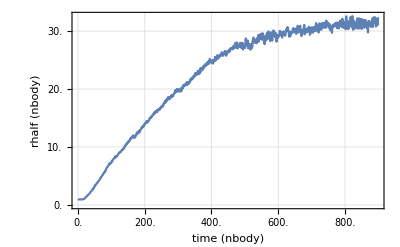

```mathematica
meanRhalfAndTimePlot=ScaledListPlot[meanRhalfAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rhalf (nbody)","rhalf (pc)"},{"time (nbody)","time (My)"}},
"ShowAllScales"->True]
```

### Mean rdens

```mathematica
meanRdens=Mean/@DeleteCases[Transpose[data[[All,All,3]]],$Failed,{2}];
```

```mathematica
meanRdensAndTime=Transpose[{timeArray,meanRdens}];
```

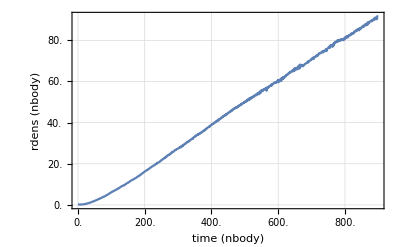

```mathematica
meanRdensAndTimePlot=ScaledListPlot[meanRdensAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rdens (nbody)","rdens (pc)"},{"time (nbody)","time (My)"}},"ShowAllScales"->True]
```

## Loading Data

#### Load from OUT3 or MX

```mathematica
(* 8 values: id, pos, vel, mass *)
(* 8 bytes each one *)
```

```mathematica
(numberOfStars*maxNbodyTime*runmax*8*8)/(1024*1024*1024. nbodyStep)
```

3.00074

```mathematica
snapshots=All;
```

```mathematica
(*snapshots=Range[1,maxNbodyTime,10];*)
```

```mathematica
Write[logstream, "computing particles.mx ...."]
```

```mathematica
(* Check also: "particles.bin" *)
If[!FileExistsQ["particles.mx"]
	,
	Print[TimeAndMem[]];
	(*While[Kernels[] == {}, 
		kernels = LaunchKernels[];
		];*)
	kernels = LaunchKernels[];
	Write[logstream, kernels];
	Print["Kernels: ", kernels];
	SetSharedVariable[dirs];
	ParallelEvaluate[AppendTo[$Path, Environment["MYGITDIR"]]];
	ParallelEvaluate[SetDirectory[resultsPath]];
	ParallelNeeds["AstroTools`nbody6`"];
	ParallelNeeds["AstroTools`Utilities`"];
	(particles = 
		Transpose@
		ParallelTable[
			SetDirectory[dirs[[i]]];
			Print["DIR: ", dirs[[i]]];
			{bodys,xs,vs,name} = Flatten[ReadOUT3["OUT3","Snapshots" -> snapshots], 1];
			xs=Partition[#,3]&/@xs;
			vs=Partition[#,3]&/@vs;
			ResetDirectory[]; 
			{bodys,xs,vs,name}
			,
			{i,1,Length[dirs]}]);
	
	Print["Closing kernels ..."];
	CloseKernels[];

	(*-- SAVE to a MX file --*)
	Print["Saving data to MX ... "];
	Print[TimeAndMem[]];
	DumpSave["particles.mx", particles];
	Print[TimeAndMem[]];

	(*-- SAVE to a BIN file --*)
	(* BinarySerializeSave[particles,"particles.bin"]; // AbsoluteTiming *)
	
	,
	
	(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["particles.mx"];
] // AbsoluteTiming
```

18:02:10 mem:187.655MB

Kernels: {KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

DIR: ./run-100/

DIR: ./run-111/

DIR: ./run-122/

DIR: ./run-135/

DIR: ./run-149/

DIR: ./run-156/

DIR: ./run-161/

DIR: ./run-16/

DIR: ./run-198/

DIR: ./run-213/

DIR: ./run-233/

DIR: ./run-24/

DIR: ./run-259/

DIR: ./run-272/

DIR: ./run-283/

DIR: ./run-290/

DIR: ./run-306/

DIR: ./run-318/

DIR: ./run-334/

DIR: ./run-349/

DIR: ./run-354/

DIR: ./run-365/

DIR: ./run-374/

DIR: ./run-38/

DIR: ./run-404/

DIR: ./run-412/

DIR: ./run-420/

DIR: ./run-442/

DIR: ./run-453/

DIR: ./run-464/

DIR: ./run-390/

DIR: ./run-136/

DIR: ./run-405/

DIR: ./run-383/

DIR: ./run-284/

DIR: ./run-252/

DIR: ./run-423/

DIR: ./run-157/

DIR: ./run-219/

DIR: ./run-113/

DIR: ./run-124/

DIR: ./run-163/

DIR: ./run-264/

DIR: ./run-34/

DIR: ./run-329/

DIR: ./run-1/

DIR: ./run-444/

DIR: ./run-275/

DIR: ./run-416/

DIR: ./run-454/

DIR: ./run-101/

DIR: ./run-465/

DIR: ./run-239/

DIR: ./run-292/

DIR: ./run-173/

DIR: ./run-152/

DIR: ./run-357/

DIR: ./run-337/

DIR: ./run-310/

DIR: ./run-366/

DIR: ./run-396/

DIR: ./run-253/

DIR: ./run-140/

DIR: ./run-158/

DIR: ./run-428/

DIR: ./run-407/

DIR: ./run-288/

DIR: ./run-229/

DIR: ./run-120/

DIR: ./run-131/

DIR: ./run-384/

DIR: ./run-350/

DIR: ./run-265/

DIR: ./run-44/

DIR: ./run-165/

DIR: ./run-203/

DIR: ./run-153/

DIR: ./run-418/

DIR: ./run-277/

DIR: ./run-243/

DIR: ./run-331/

DIR: ./run-339/

DIR: ./run-298/

DIR: ./run-456/

DIR: ./run-467/

DIR: ./run-181/

DIR: ./run-358/

DIR: ./run-106/

DIR: ./run-370/

DIR: ./run-312/

DIR: ./run-400/

DIR: ./run-160/

DIR: ./run-441/

DIR: ./run-256/

DIR: ./run-146/

DIR: ./run-232/

DIR: ./run-289/

DIR: ./run-409/

DIR: ./run-385/

DIR: ./run-268/

DIR: ./run-121/

DIR: ./run-450/

DIR: ./run-351/

DIR: ./run-132/

DIR: ./run-189/

DIR: ./run-280/

DIR: ./run-302/

DIR: ./run-154/

DIR: ./run-468/

DIR: ./run-246/

DIR: ./run-169/

DIR: ./run-460/

DIR: ./run-333/

DIR: ./run-209/

DIR: ./run-419/

DIR: ./run-347/

DIR: ./run-361/

DIR: ./run-372/

DIR: ./run-110/

DIR: ./run-314/

DIR: ./run-472/

DIR: ./run-47/

DIR: ./run-488/

DIR: ./run-49/

DIR: ./run-506/

DIR: ./run-518/

DIR: ./run-530/

DIR: ./run-555/

DIR: ./run-565/

DIR: ./run-576/

DIR: ./run-592/

DIR: ./run-607/

DIR: ./run-623/

DIR: ./run-639/

DIR: ./run-656/

DIR: ./run-669/

DIR: ./run-680/

DIR: ./run-690/

DIR: ./run-695/

DIR: ./run-69/

DIR: ./run-707/

DIR: ./run-713/

DIR: ./run-719/

DIR: ./run-724/

DIR: ./run-72/

DIR: ./run-733/

DIR: ./run-739/

DIR: ./run-77/

DIR: ./run-89/

DIR: ./run-93/

DIR: ./run-66/

DIR: ./run-491/

DIR: ./run-737/

DIR: ./run-8/

DIR: ./run-658/

DIR: ./run-537/

DIR: ./run-614/

DIR: ./run-731/

DIR: ./run-693/

DIR: ./run-559/

DIR: ./run-82/

DIR: ./run-725/

DIR: ./run-71/

DIR: ./run-568/

DIR: ./run-519/

DIR: ./run-711/

DIR: ./run-474/

DIR: ./run-6/

DIR: ./run-697/

DIR: ./run-480/

DIR: ./run-742/

DIR: ./run-593/

DIR: ./run-683/

DIR: ./run-627/

DIR: ./run-63/

DIR: ./run-716/

DIR: ./run-4/

DIR: ./run-94/

DIR: ./run-50/

DIR: ./run-579/

DIR: ./run-738/

DIR: ./run-661/

DIR: ./run-497/

DIR: ./run-67/

DIR: ./run-541/

DIR: ./run-694/

DIR: ./run-61/

DIR: ./run-722/

DIR: ./run-88/

DIR: ./run-91/

DIR: ./run-569/

DIR: ./run-732/

DIR: ./run-563/

DIR: ./run-712/

DIR: ./run-485/

DIR: ./run-728/

DIR: ./run-522/

DIR: ./run-703/

DIR: ./run-603/

DIR: ./run-76/

DIR: ./run-68/

DIR: ./run-475/

DIR: ./run-698/

DIR: ./run-645/

DIR: ./run-501/

DIR: ./run-630/

DIR: ./run-717/

DIR: ./run-99/

DIR: ./run-512/

DIR: ./run-580/

DIR: ./run-478/

DIR: ./run-486/

DIR: ./run-499/

DIR: ./run-503/

DIR: ./run-513/

DIR: ./run-528/

DIR: ./run-551/

DIR: ./run-564/

DIR: ./run-574/

DIR: ./run-584/

DIR: ./run-606/

DIR: ./run-621/

DIR: ./run-635/

DIR: ./run-655/

Closing kernels ...

Saving data to MX ...

18:06:52 mem:13.1426GB

18:32:35 mem:9.51514GB

{1825.46,Null}

```mathematica
Write[logstream, "particles.mx done!"]
```

```mathematica
(* --- serial computation ---
(particles=
Transpose@
Table[SetDirectory[dirs[[i]]];
Print["DIR: ", dirs[[i]]];
{bodys,xs,vs,name}=Flatten[ReadOUT3["OUT3","Snapshots"->All],1];
xs=Partition[#,3]&/@xs;
vs=Partition[#,3]&/@vs;
ResetDirectory[]; 
{bodys,xs,vs,name}
,{i,1,Length[dirs]}]);//AbsoluteTiming *)
```

#### Mem information

```mathematica
TimeAndMem[]
```

18:32:35 mem:9.51514GB

```mathematica
(*PrintArrayInfo[particles]*)
```

```mathematica
DeleteOuts[500]
```

session mem: 9.51515GB

No Out[] greater than 500MB

```mathematica
$numberOfRunsStatus=Dimensions[particles][[2]]
```

224

## Filtering Invalid Data

### Indexes To Extract Data

```mathematica
nbIndexes=Table[Range[maxNbodyTime/nbodyStep+1],{runmax}];
```

```mathematica
nbIndexes//Dimensions
```

{224,900}

```mathematica
nbIndexes[[1]]//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900}

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900}

### Incomplete runs

```mathematica
particles//Dimensions
```

{4,224,900}

```mathematica
Length/@particles[[4]]//Union
```

{900}

```mathematica
(* delete runs that have not complete data *)
maxtimes=Length/@particles[[4]]
```

{900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900}

```mathematica
delPos1=Position[maxtimes,x_/;x<Max[maxtimes]]
```

{}

```mathematica
delPos1//Length
```

0

#### FIX: Delete complete runs

```mathematica
Extract[dirs,delPos1]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos1],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete
```

{}

Opt – Update variables to continue computing

```mathematica
particles//Dimensions
```

{4,224,900}

```mathematica
dirs=Delete[dirs,delPos1];
runmax=Length[dirs];
particles=Delete[#, delPos1]&/@particles;
nbIndexes=Delete[nbIndexes, delPos1];
nbLenIndexes=Length/@nbIndexes;
parameters=Delete[parameters, delPos1];
```

```mathematica
particles//Dimensions
```

{4,224,900}

```mathematica
nbIndexes//Length
```

224

```mathematica
parameters//Dimensions
```

{224,6}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 13.6991GB

### Particles in the same position

#### TEST

```mathematica
particles[[All,All,All,1;;numberOfStars]]//Dimensions
```

{4,224,900,250}

```mathematica
Clear[ceros];
If[!FileExistsQ["ceros.mx"],
ceros=Reap[
Do[
Print["run: ", run];
Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}];Print["CERO AT: ", run];Break[]]
]
,{t,1,nbLenIndexes[[run]]}
],
{run,1,runmax}]
];
DumpSave["ceros.mx", ceros]
,
(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["ceros.mx"];
];//AbsoluteTiming
```

run: 1

run: 2

run: 3

run: 4

run: 5

run: 6

run: 7

run: 8

run: 9

run: 10

run: 11

run: 12

run: 13

run: 14

run: 15

run: 16

run: 17

run: 18

run: 19

run: 20

run: 21

run: 22

run: 23

run: 24

run: 25

run: 26

run: 27

run: 28

run: 29

run: 30

run: 31

run: 32

run: 33

run: 34

run: 35

run: 36

run: 37

run: 38

run: 39

run: 40

run: 41

run: 42

run: 43

run: 44

run: 45

run: 46

run: 47

run: 48

run: 49

run: 50

run: 51

run: 52

run: 53

run: 54

run: 55

run: 56

run: 57

run: 58

run: 59

run: 60

run: 61

run: 62

run: 63

run: 64

run: 65

run: 66

run: 67

run: 68

run: 69

run: 70

run: 71

run: 72

run: 73

run: 74

run: 75

run: 76

run: 77

run: 78

run: 79

run: 80

run: 81

run: 82

run: 83

run: 84

run: 85

run: 86

run: 87

run: 88

run: 89

run: 90

run: 91

run: 92

run: 93

run: 94

run: 95

run: 96

run: 97

run: 98

run: 99

run: 100

run: 101

run: 102

run: 103

run: 104

run: 105

run: 106

run: 107

run: 108

run: 109

run: 110

run: 111

run: 112

run: 113

run: 114

run: 115

run: 116

run: 117

run: 118

run: 119

run: 120

run: 121

run: 122

run: 123

run: 124

run: 125

run: 126

run: 127

run: 128

run: 129

run: 130

run: 131

run: 132

run: 133

run: 134

run: 135

run: 136

run: 137

run: 138

run: 139

run: 140

run: 141

run: 142

run: 143

run: 144

run: 145

run: 146

run: 147

run: 148

run: 149

run: 150

run: 151

run: 152

run: 153

run: 154

run: 155

run: 156

run: 157

run: 158

run: 159

run: 160

run: 161

run: 162

run: 163

run: 164

run: 165

run: 166

run: 167

run: 168

run: 169

run: 170

run: 171

run: 172

run: 173

run: 174

run: 175

run: 176

run: 177

run: 178

run: 179

run: 180

run: 181

run: 182

run: 183

run: 184

run: 185

run: 186

run: 187

run: 188

run: 189

run: 190

run: 191

run: 192

run: 193

run: 194

run: 195

run: 196

run: 197

run: 198

run: 199

run: 200

run: 201

run: 202

run: 203

run: 204

run: 205

run: 206

run: 207

run: 208

run: 209

run: 210

run: 211

run: 212

run: 213

run: 214

run: 215

run: 216

run: 217

run: 218

run: 219

run: 220

run: 221

run: 222

run: 223

run: 224

{946.239,Null}

```mathematica
ceros[[2]]
```

{}

#### Double check

```mathematica
(*invalid=With[{run=7},Reap[Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}]]
]
,{t,1,nbLenIndexes[[run]]}
]]
];*)
```

```mathematica
(*invalid//Short*)
```

```mathematica
(*With[{run=7, time=1100},
Select[GatherBy[Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}],Last],Length[#]>1&]]*)
```

```mathematica
(*With[
{part1=2,
part2=1,
run=46,
interTime=220
},
vel=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[3,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];
pos=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];

{ListLinePlot[{Norm/@vel[[All,1]],Norm/@vel[[All,2]]},
PlotRange->{{0,1000},{0,100}}],
ListLinePlot[{Norm/@pos[[All,1]],Norm/@pos[[All,2]]},
PlotRange->{{0,1000},{0,50000}},Epilog->InfiniteLine[{{interTime,0},{interTime,1}}]]}
]*)
```

```mathematica
(* testing indexes outside particles range *)
```

```mathematica
(*testing1001=Table[#[1001]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*Position[testimg1001,_Missing]*)
```

```mathematica
(*testing1002=Table[#[1002]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*testing1002[[8]]*)
```

#### FIX 1: Delete complete runs

```mathematica
delPos2=If[ceros[[2]]=={},{},Partition[Union[ceros[[2,1]][[All,1]]],1]];
```

```mathematica
delPos2//Short
```

{}

```mathematica
Extract[dirs,delPos2]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos2],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

(* 
	Si dirsToDelete≠0 borrar *.m *.mx 
	generar goodRuns.log y correr nb de nuevo.
*)

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos2];
```

```mathematica
runmax=Length[dirs]
```

224

```mathematica
particles//Dimensions
```

{4,224,900}

```mathematica
particles=Delete[#, delPos2]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,224,900}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 13.6991GB

```mathematica
nbIndexes=Delete[nbIndexes, delPos2];
```

```mathematica
nbIndexes//Length
```

224

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900}

```mathematica
parameters//Dimensions
```

{224,6}

```mathematica
parameters=Delete[parameters, delPos2];
```

```mathematica
parameters//Dimensions
```

{224,6}

#### FIX 2: Delete specific snapshots (ruled out)

```mathematica
(* We will delete data only for snapshots containg equal positions *)
```

delPos3 = ceros[[2, 1]]

particles = Delete[#, delPos3] & /@ particles;

timeIndexes[[1, 450]]

Complement[Range[1000], timeIndexes[[1]]]

timeIndexes = Delete[timeIndexes, delPos3];

Complement[Range[1000], timeIndexes[[1]]]

nbLenIndexes = Length /@ timeIndexes

### Particles with index 0 / position 0.

#### TEST

```mathematica
(* Delete time snaphots of incorrect data with ceros in the position vector. *)
(* Very strange issue from nbody *)
```

```mathematica
delPos4=Position[particles[[4]],0][[All,{1,2}]];
```

```mathematica
delPos4//Short
```

{{2,151},{2,152},{4,102},{4,103},{4,105},{4,280},{4,490},{4,491},{4,492},{4,493},{4,494},{4,495},{4,496},{11,54},{11,186},{13,731},{13,732},{13,733},{13,734},{13,735},{13,736},{19,262},{19,263},{19,264},{19,265},{19,266},{19,267},{19,268},{21,84},{27,150},{27,562},{28,76},{28,643},{28,644},{28,895},{28,896},{28,897},{28,898},{28,899},{28,900},{30,63},{33,84},{34,41},{34,152},{34,253},{34,487},{34,488},{34,865},{34,866},{34,867},{39,128},{39,129},{39,130},{39,131},{39,132},{39,133},{39,134},{39,135},{39,136},{39,137},{39,138},{39,139},{39,140},{39,141},{39,142},{39,143},{39,144},{39,145},{39,146},{39,147},{39,148},{40,48},{40,257},{40,258},{45,368},{50,506},{50,507},{50,508},{50,509},{50,510},{50,511},{50,512},{50,513},{50,514},{50,515},{50,516},{50,517},{50,518},{50,519},{50,520},{50,521},{50,522},{50,523},{50,524},{50,525},{50,526},{50,527},{50,528},{50,529},{50,530},{50,531},{50,532},{50,533},{50,534},{50,535},{50,536},{50,537},{50,538},{50,539},{50,540},{50,541},{50,542},{50,543},{50,544},{50,545},{56,41},{58,128},{58,129},{58,130},{58,131},{58,132},{58,133},{58,134},{58,135},{58,136},{58,137},{58,138},{58,139},{58,140},{58,141},{58,142},{58,143},{58,144},{58,145},{58,146},{58,147},{58,148},{58,149},{58,150},{58,151},{58,152},{58,153},{58,154},{58,155},{58,156},{58,157},{58,158},{58,159},{58,160},{58,161},{58,162},{58,163},{58,164},{58,165},{58,166},{58,167},{58,168},{58,169},{58,170},{58,171},{58,172},{58,173},{58,174},{58,175},{58,176},{58,177},{58,178},{58,179},{58,180},{58,181},{58,182},{58,183},{58,184},{58,185},{58,186},{58,187},{58,188},{58,189},{58,190},{58,191},{58,192},{58,193},{58,194},{58,195},{58,196},{58,197},{58,198},{58,199},{58,200},{58,201},{58,202},{58,203},{58,204},{58,205},{58,206},{58,207},{58,208},{58,209},{58,210},{58,211},{58,212},{58,213},{58,214},{58,215},{58,216},{58,217},{58,218},{58,219},{58,220},{58,221},{58,222},{58,223},{58,224},{58,225},{58,226},{58,227},{58,228},{58,229},{58,230},{58,231},{58,232},{58,233},{58,234},{58,235},{58,236},{58,237},{58,238},{58,239},{58,240},{58,241},{58,242},{58,243},{58,244},{58,245},{58,246},{58,247},{58,248},{58,249},{58,250},{58,251},{58,252},{58,253},{58,254},{58,255},{58,256},{58,257},{58,258},{58,259},{58,260},{58,261},{58,262},{58,263},{58,264},{58,265},{58,266},{58,267},{58,268},{58,269},{58,270},{58,271},{58,272},{58,273},{58,274},{58,275},{58,276},{58,277},{58,278},{58,279},{58,280},{58,281},{58,282},{58,283},{58,284},{58,285},{58,286},{58,287},{58,288},{58,289},{58,290},{58,291},{58,292},{58,293},{58,294},{58,295},{58,296},{58,297},{58,298},{58,299},{58,300},{58,301},{58,302},{58,303},{58,304},{58,305},{58,306},{58,307},{58,308},{58,309},{58,310},{58,311},{58,312},{58,313},{58,314},{58,315},{58,316},{58,317},{58,318},{58,319},{58,320},{58,321},{58,322},{58,323},{58,324},{58,325},{58,326},{58,327},{58,328},{58,329},{58,330},{58,331},{58,332},{58,333},{58,334},{58,335},{58,336},{58,337},{58,338},{58,339},{58,340},{58,341},{58,342},{58,343},{58,344},{58,345},{58,346},{58,347},{58,348},{58,349},{58,350},{58,351},{58,352},{58,353},{58,354},{58,355},{58,356},{58,357},{58,358},{58,359},{58,360},{58,361},{58,362},{58,363},{58,364},{58,365},{58,366},{58,367},{58,368},{58,369},{58,370},{58,371},{58,372},{58,373},{58,374},{58,375},{58,376},{58,377},{58,378},{58,379},{58,380},{58,381},{58,382},{58,383},{58,384},{58,385},{58,386},{58,387},{58,388},{58,389},{58,390},{58,391},{58,392},{58,393},{58,394},{58,395},{58,396},{58,397},{58,398},{58,399},{58,400},{58,401},{58,402},{58,403},{58,404},{58,405},{58,406},{58,407},{58,408},{58,409},{58,410},{58,411},{58,412},{58,413},{58,414},{58,415},{58,416},{58,417},{58,418},{58,419},{58,420},{58,421},{58,422},{58,423},{58,424},{58,425},{58,426},{58,427},{58,428},{58,429},{58,430},{58,431},{58,432},{58,433},{58,434},{58,435},{58,436},{58,437},{58,438},{58,439},{58,440},{58,441},{58,442},{58,443},{58,444},{58,445},{58,446},{58,447},{58,448},{58,449},{58,450},{58,451},{58,452},{58,453},{58,454},{58,455},{58,456},{58,457},{58,458},{58,459},{58,460},{58,461},{58,462},{58,463},{58,464},{58,465},{58,466},{58,467},{58,468},{58,469},{58,470},{58,471},{58,472},{58,473},{58,474},{58,475},{58,476},{58,477},{58,478},{58,479},{58,480},{58,481},{58,482},{58,483},{58,484},{58,485},{58,486},{58,487},{58,488},{58,489},{58,490},{58,491},{58,492},{58,493},{58,494},{58,495},{58,496},{58,497},{58,498},{58,499},{58,500},{58,501},{58,502},{58,503},{58,504},{58,505},{58,506},{58,507},{58,508},{58,509},{58,510},{58,511},{58,512},{58,513},{58,514},{58,515},{58,516},{58,517},{58,518},{58,519},{58,520},{58,521},{58,522},{58,523},{58,524},{58,525},{58,526},{58,527},{58,528},{58,529},{58,530},{58,531},{58,532},{58,533},{58,534},{58,535},{58,536},{58,537},{58,538},{58,539},{58,540},{58,541},{58,542},{58,543},{58,544},{58,545},{58,546},{58,547},{58,548},{58,549},{58,550},{58,551},{58,552},{58,553},{58,554},{58,555},{58,556},{58,557},{58,558},{58,559},{58,560},{58,561},{58,562},{58,563},{58,564},{58,565},{58,566},{58,567},{58,568},{58,569},{58,570},{58,571},{58,572},{58,573},{58,574},{58,575},{58,576},{58,577},{58,578},{58,579},{58,580},{58,581},{58,582},{58,583},{58,584},{58,585},{58,586},{58,587},{58,588},{58,589},{58,590},{58,591},{58,592},{58,593},{58,594},{58,595},{58,596},{58,597},{58,598},{58,599},{58,600},{58,601},{58,602},{58,603},{58,604},{58,605},{58,606},{58,607},{58,608},{58,609},{58,610},{58,611},{58,612},{58,613},{58,614},{58,615},{58,616},{58,617},{58,618},{58,619},{58,620},{58,621},{58,622},{58,623},{58,624},{58,625},{58,626},{58,627},{58,628},{58,629},{58,630},{58,631},{58,632},{58,633},{58,634},{58,635},{58,636},{58,637},{58,638},{58,639},{58,640},{58,641},{58,642},{58,643},{58,644},{58,645},{58,646},{58,647},{58,648},{58,649},{58,650},{58,651},{58,652},{58,653},{58,654},{58,655},{58,656},{58,657},{58,658},{58,659},{58,660},{58,661},{58,662},{58,663},{58,664},{58,665},{58,666},{58,667},{58,668},{58,669},{58,670},{58,671},{58,672},{58,673},{58,674},{58,675},{58,676},{58,677},{58,678},{58,679},{58,680},{58,681},{58,682},{58,683},{58,684},{58,685},{58,686},{58,687},{58,688},{58,689},{58,690},{58,691},{58,692},{58,693},{58,694},{58,695},{58,696},{58,697},{58,698},{58,699},{58,700},{58,701},{58,702},{58,703},{58,704},{58,705},{58,706},{58,707},{58,708},{58,709},{58,710},{58,711},{58,712},{58,713},{58,714},{58,715},{58,716},{58,717},{58,718},{58,719},{58,720},{58,721},{58,722},{58,723},{58,724},{58,725},{58,726},{58,727},{58,728},{58,729},{58,730},{58,731},{58,732},{58,733},{58,734},{58,735},{58,736},{58,737},{58,738},{58,739},{58,740},{58,741},{58,742},{58,743},{58,744},{58,745},{58,746},{58,747},{58,748},{58,749},{58,750},{58,751},{58,752},{58,753},{58,754},{58,755},{58,756},{58,757},{58,758},{58,759},{58,760},{58,761},{58,762},{58,763},{58,764},{58,765},{58,766},{58,767},{58,768},{58,769},{58,770},{58,771},{58,772},{58,773},{58,774},{58,775},{58,776},{58,777},{58,778},{58,779},{58,780},{58,781},{58,782},{58,783},{58,784},{58,785},{58,786},{58,787},{58,788},{58,789},{58,790},{58,791},{58,792},{58,793},{58,794},{58,795},{58,796},{58,797},{58,798},{58,799},{58,800},{58,801},{58,802},{58,803},{58,804},{58,805},{58,806},{58,807},{58,808},{58,809},{58,810},{58,811},{58,812},{58,813},{58,814},{58,815},{58,816},{58,817},{58,818},{58,819},{58,820},{58,821},{58,822},{58,823},{58,824},{58,825},{58,826},{58,827},{58,828},{58,829},{58,830},{58,831},{58,832},{58,833},{58,834},{58,835},{58,836},{58,837},{58,838},{58,839},{58,840},{58,841},{58,842},{58,843},{58,844},{58,845},{58,846},{58,847},{58,848},{58,849},{58,850},{58,851},{58,852},{58,853},{58,854},{58,855},{58,856},{58,857},{58,858},{58,859},{58,860},{58,861},{58,862},{58,863},{58,864},{58,865},{58,866},{58,867},{58,868},{58,869},{58,870},{58,871},{58,872},{58,873},{58,874},{58,875},{58,876},{58,877},{58,878},{58,879},{58,880},{58,881},{58,882},{58,883},{58,884},{58,885},{58,886},{58,887},{58,888},{58,889},{58,890},{58,891},{58,892},{58,893},{58,894},{58,895},{58,896},{58,897},{58,898},{58,899},{58,900},{60,194},{60,195},{60,196},{60,197},{60,198},{60,199},{60,200},{60,201},{60,202},{60,203},{60,204},{60,205},{60,206},{60,207},{60,208},{60,209},{60,210},{60,211},{60,212},{60,213},{60,214},{60,215},{60,216},{60,217},{60,218},{60,219},{60,220},{60,221},{60,222},{60,223},{60,224},{60,225},{60,226},{60,227},{60,228},{60,229},{60,230},{60,231},{60,232},{60,233},{60,234},{60,235},{60,236},{60,237},{60,238},{60,239},{60,240},{60,241},{60,242},{60,243},{60,244},{60,245},{60,246},{60,247},{60,248},{60,249},{60,250},{60,251},{60,252},{60,253},{60,254},{60,255},{60,256},{60,257},{60,258},{60,259},{60,260},{60,261},{60,262},{60,263},{60,264},{60,265},{60,266},{60,267},{60,268},{60,269},{60,270},{60,271},{60,272},{60,273},{60,274},{60,275},{60,276},{60,277},{60,278},{60,279},{60,280},{60,281},{60,282},{60,283},{60,284},{60,285},{60,286},{60,287},{60,288},{60,289},{60,290},{60,291},{60,292},{60,293},{60,294},{60,295},{60,296},{60,297},{60,298},{60,299},{60,300},{60,301},{60,302},{60,303},{60,304},{60,305},{60,306},{60,307},{60,308},{60,309},{60,310},{60,311},{60,312},{60,313},{60,314},{60,315},{60,316},{60,317},{60,318},{60,319},{60,320},{60,321},{60,322},{60,323},{60,324},{60,325},{60,326},{60,327},{60,328},{60,329},{60,330},{60,331},{60,332},{60,333},{60,334},{60,335},{60,336},{60,337},{60,338},{60,339},{60,340},{60,341},{60,342},{60,343},{60,344},{60,345},{60,346},{60,347},{60,348},{60,349},{60,350},{60,351},{60,352},{60,353},{60,354},{60,355},{60,356},{60,357},{60,358},{60,359},{60,360},{60,361},{60,362},{60,363},{60,364},{60,365},{60,366},{60,367},{60,368},{60,369},{60,370},{60,371},{60,372},{60,373},{60,374},{60,375},{60,376},{60,377},{60,378},{60,379},{60,380},{60,381},{60,382},{60,383},{60,384},{60,385},{60,386},{60,387},{60,388},{60,389},{60,390},{60,391},{60,392},{60,393},{60,394},{60,395},{60,396},{60,397},{60,398},{60,399},{60,400},{60,401},{60,402},{60,403},{60,404},{60,405},{60,406},{60,407},{60,408},{60,409},{60,410},{60,411},{60,412},{60,413},{60,414},{60,415},{60,416},{60,417},{60,418},{60,419},{60,420},{60,421},{60,422},{60,423},{60,424},{60,425},{60,426},{60,427},{60,428},{60,429},{60,430},{60,431},{60,432},{60,433},{60,434},{60,435},{60,436},{60,437},{60,438},{60,439},{60,440},{60,441},{60,442},{60,443},{60,444},{60,445},{60,446},{60,447},{60,448},{60,449},{60,450},{60,451},{60,452},{60,453},{60,454},{60,455},{60,456},{60,457},{60,458},{60,459},{60,460},{60,461},{60,462},{60,463},{60,464},{60,465},{60,466},{60,467},{60,468},{60,469},{60,470},{60,471},{60,472},{60,473},{60,474},{60,475},{60,476},{60,477},{60,478},{60,479},{60,480},{60,481},{60,482},{60,483},{60,484},{60,485},{60,486},{60,487},{60,488},{60,489},{60,490},{60,491},{60,492},{60,493},{60,494},{60,495},{60,496},{60,497},{60,498},{60,499},{60,500},{60,501},{60,502},{60,503},{60,504},{60,505},{60,506},{60,507},{60,508},{60,509},{60,510},{60,511},{60,512},{60,513},{60,514},{60,515},{60,516},{60,517},{60,518},{60,519},{60,520},{60,521},{60,522},{60,523},{60,524},{60,525},{60,526},{60,527},{60,528},{60,529},{60,530},{60,531},{60,532},{60,533},{60,534},{60,535},{60,536},{60,537},{60,538},{60,539},{60,540},{60,541},{60,542},{60,543},{60,544},{60,545},{60,546},{60,547},{60,548},{60,549},{60,550},{60,551},{60,552},{60,553},{60,554},{60,555},{60,556},{60,557},{60,558},{60,559},{60,560},{60,561},{60,562},{60,563},{60,564},{60,565},{60,566},{60,567},{60,568},{60,569},{60,570},{60,571},{60,572},{60,573},{60,574},{60,575},{60,576},{60,577},{60,578},{60,579},{60,580},{60,581},{60,582},{60,583},{60,584},{60,585},{60,586},{60,587},{60,588},{60,589},{60,590},{60,591},{60,592},{60,593},{60,594},{60,595},{60,596},{60,597},{60,598},{60,599},{60,600},{60,601},{60,602},{60,603},{60,604},{60,605},{60,606},{60,607},{60,608},{60,609},{60,610},{60,611},{60,612},{60,613},{60,614},{60,615},{60,616},{60,617},{60,618},{60,619},{60,620},{60,621},{60,622},{60,623},{60,624},{60,625},{60,626},{60,627},{60,628},{60,629},{60,630},{60,631},{60,632},{60,633},{60,634},{60,635},{60,636},{60,637},{60,638},{60,639},{60,640},{60,641},{60,642},{60,643},{60,644},{60,645},{60,646},{60,647},{60,648},{60,649},{60,650},{60,651},{60,652},{60,653},{60,654},{60,655},{60,656},{60,657},{60,658},{60,659},{60,660},{60,661},{60,662},{60,663},{60,664},{60,665},{60,666},{60,667},{60,668},{60,669},{60,670},{60,671},{60,672},{60,673},{60,674},{60,675},{60,676},{60,677},{60,678},{60,679},{60,680},{60,681},{60,682},{60,683},{60,684},{60,685},{60,686},{60,687},{60,688},{60,689},{60,690},{60,691},{60,692},{60,693},{60,694},{60,695},{60,696},{60,697},{60,698},{60,699},{60,700},{60,701},{60,702},{60,703},{60,704},{60,705},{60,706},{60,707},{60,708},{60,709},{60,710},{60,711},{60,712},{60,713},{60,714},{60,715},{60,716},{60,717},{60,718},{60,719},{60,720},{60,721},{60,722},{60,723},{60,724},{60,725},{60,726},{60,727},{60,728},{60,729},{60,730},{60,731},{60,732},{60,733},{60,734},{60,735},{60,736},{60,737},{60,738},{60,739},{60,740},{60,741},{60,742},{60,743},{60,744},{60,745},{60,746},{60,747},{60,748},{60,749},{60,750},{60,751},{60,752},{60,753},{60,754},{60,755},{60,756},{60,757},{60,758},{60,759},{60,760},{60,761},{60,762},{60,763},{60,764},{60,765},{60,766},{60,767},{60,768},{60,769},{60,770},{60,771},{60,772},{60,773},{60,774},{60,775},{60,776},{60,777},{60,778},{60,779},{60,780},{60,781},{60,782},{60,783},{60,784},{60,785},{60,786},{60,787},{60,788},{60,789},{60,790},{60,791},{60,792},{60,793},{60,794},{60,795},{60,796},{60,797},{60,798},{60,799},{60,800},{60,801},{60,802},{60,803},{60,804},{60,805},{60,806},{60,807},{60,808},{60,809},{60,810},{60,811},{60,812},{60,813},{60,814},{60,815},{60,816},{60,817},{60,818},{60,819},{60,820},{60,821},{60,822},{60,823},{60,824},{60,825},{60,826},{60,827},{60,828},{60,829},{60,830},{60,831},{60,832},{60,833},{60,834},{60,835},{60,836},{60,837},{60,838},{60,839},{60,840},{60,841},{60,842},{60,843},{60,844},{60,845},{60,846},{60,847},{60,848},{60,849},{60,850},{60,851},{60,852},{60,853},{60,854},{60,855},{60,856},{60,857},{60,858},{60,859},{60,860},{60,861},{60,862},{60,863},{60,864},{60,865},{60,866},{60,867},{60,868},{60,869},{60,870},{60,871},{60,872},{60,873},{60,874},{60,875},{60,876},{60,877},{60,878},{60,879},{60,880},{60,881},{60,882},{60,883},{60,884},{60,885},{60,886},{60,887},{60,888},{60,889},{60,890},{60,891},{60,892},{60,893},{60,894},{60,895},{60,896},{60,897},{60,898},{60,899},{60,900},{62,163},{66,64},{68,53},{68,105},{68,193},{68,357},{68,435},{68,601},{68,602},{68,603},{68,604},{68,605},{68,606},{68,607},{68,608},{70,22},{73,29},{73,33},{77,214},{77,370},{78,75},{78,97},{78,302},{78,303},{78,504},{78,505},{82,28},{89,33},{89,101},{90,477},{90,478},{90,479},{90,480},{90,481},{90,482},{91,169},{91,185},{91,187},{91,280},{91,281},{98,19},{98,255},{98,256},{98,257},{98,258},{98,259},{98,260},{101,44},{101,65},{101,237},{101,238},{101,239},{101,240},{101,241},{101,242},{101,243},{101,244},{101,245},{101,246},{101,247},{101,248},{101,249},{101,250},{101,251},{101,252},{101,253},{101,254},{101,255},{101,256},{101,257},{101,258},{101,259},{101,260},{101,261},{101,262},{101,263},{101,264},{101,265},{101,266},{101,267},{101,268},{101,269},{101,270},{101,271},{101,272},{101,273},{101,274},{101,275},{101,276},{101,277},{101,278},{101,279},{101,280},{101,281},{101,282},{101,283},{101,284},{101,285},{101,286},{101,287},{101,288},{101,289},{101,290},{101,291},{101,292},{101,293},{101,294},{101,295},{101,296},{101,297},{101,298},{101,299},{101,300},{101,301},{101,302},{101,303},{101,304},{101,305},{101,306},{101,307},{101,308},{101,309},{101,310},{101,311},{101,312},{101,313},{101,314},{101,315},{101,316},{101,317},{101,318},{101,319},{101,320},{101,321},{101,322},{101,323},{101,324},{101,325},{101,326},{101,327},{101,328},{101,329},{101,330},{101,331},{101,332},{101,333},{101,334},{101,335},{101,336},{101,337},{101,338},{101,339},{101,340},{101,341},{101,342},{101,343},{101,344},{101,345},{101,346},{101,347},{101,348},{101,349},{101,350},{101,351},{101,352},{101,353},{101,354},{101,355},{101,356},{101,357},{101,358},{101,359},{101,360},{101,361},{101,362},{101,363},{101,364},{101,365},{101,366},{101,367},{101,368},{101,369},{101,370},{101,371},{101,372},{101,373},{101,374},{101,375},{101,376},{101,377},{101,378},{101,379},{101,380},{101,381},{101,382},{101,383},{101,384},{101,385},{101,386},{101,387},{101,388},{101,389},{101,390},{101,391},{101,392},{101,393},{101,394},{101,395},{101,396},{101,397},{101,398},{101,399},{101,400},{101,401},{101,402},{101,403},{101,404},{101,405},{101,406},{101,407},{101,408},{101,409},{101,410},{101,411},{101,412},{101,413},{101,414},{101,415},{101,416},{101,417},{101,418},{101,419},{101,420},{101,421},{101,422},{101,423},{101,424},{101,425},{101,426},{101,427},{101,428},{101,429},{101,430},{101,431},{101,432},{101,433},{101,434},{101,435},{101,436},{101,437},{101,438},{101,439},{101,440},{101,441},{101,442},{101,443},{101,444},{101,445},{101,446},{101,447},{101,448},{101,449},{101,450},{101,451},{101,452},{101,453},{101,454},{101,455},{101,456},{101,457},{101,458},{101,459},{101,460},{101,461},{101,462},{101,463},{101,464},{101,465},{101,466},{101,467},{101,468},{101,469},{101,470},{101,471},{101,472},{101,473},{101,474},{101,475},{101,476},{102,98},{107,101},{107,122},{107,145},{107,176},{107,491},{107,492},{107,493},{107,494},{107,495},{107,496},{107,497},{107,498},{107,499},{107,500},{107,501},{107,502},{107,503},{108,31},{110,56},{123,128},{123,129},{123,130},{123,131},{123,132},{123,133},{123,134},{123,135},{123,136},{123,137},{123,138},{123,139},{123,140},{123,141},{123,142},{123,143},{123,144},{123,145},{123,146},{123,147},{123,148},{125,359},{126,170},{128,52},{129,33},{129,34},{133,69},{134,91},{137,35},{139,226},{139,466},{139,467},{139,468},{139,469},{139,470},{144,18},{146,94},{147,136},{147,137},{147,138},{147,865},{147,866},{147,867},{148,743},{148,744},{148,745},{148,746},{148,747},{148,748},{148,749},{150,430},{153,231},{155,31},{156,149},{156,150},{157,104},{157,142},{157,206},{157,207},{157,208},{164,42},{167,266},{171,630},{173,125},{176,31},{183,80},{190,36},{190,67},{190,158},{190,354},{191,155},{191,156},{191,157},{191,158},{191,159},{191,160},{191,161},{191,162},{194,45},{194,132},{195,48},{196,41},{196,123},{196,124},{196,125},{196,126},{198,95},{201,72},{203,51},{204,36},{204,51},{205,42},{205,43},{205,65},{210,536},{212,366},{216,60},{216,61},{220,86},{221,62},{221,89},{223,87},{224,34},{224,91}}

```mathematica
delPos4[[All,1]]//Union
```

{2,4,11,13,19,21,27,28,30,33,34,39,40,45,50,56,58,60,62,66,68,70,73,77,78,82,89,90,91,98,101,102,107,108,110,123,125,126,128,129,133,134,137,139,144,146,147,148,150,153,155,156,157,164,167,171,173,176,183,190,191,194,195,196,198,201,203,204,205,210,212,216,220,221,223,224}

```mathematica
delPos4[[All,1]]//Union//Length
```

76

```mathematica
(* NICE runs *)
Complement[Range[runmax],delPos4[[All,1]]//Union]
```

{1,3,5,6,7,8,9,10,12,14,15,16,17,18,20,22,23,24,25,26,29,31,32,35,36,37,38,41,42,43,44,46,47,48,49,51,52,53,54,55,57,59,61,63,64,65,67,69,71,72,74,75,76,79,80,81,83,84,85,86,87,88,92,93,94,95,96,97,99,100,103,104,105,106,109,111,112,113,114,115,116,117,118,119,120,121,122,124,127,130,131,132,135,136,138,140,141,142,143,145,149,151,152,154,158,159,160,161,162,163,165,166,168,169,170,172,174,175,177,178,179,180,181,182,184,185,186,187,188,189,192,193,197,199,200,202,206,207,208,209,211,213,214,215,217,218,219,222}

```mathematica
(* Consistent with non missing IDs *)
moreIDS=Table[Position[Complement[Range[numberOfStars],#]&/@particles[[4,run,All,All]],x_/;x≠{},{1}],{run,runmax}];
Position[moreIDS,{}]//Flatten
```

{1,3,5,6,7,8,9,10,12,14,15,16,17,18,20,22,23,24,25,26,29,31,32,35,36,37,38,41,42,43,44,46,47,48,49,51,52,53,54,55,57,59,61,63,64,65,67,69,71,72,74,75,76,79,80,81,83,84,85,86,87,88,92,93,94,95,96,97,99,100,103,104,105,106,109,111,112,113,114,115,116,117,118,119,120,121,122,124,127,130,131,132,135,136,138,140,141,142,143,145,149,151,152,154,158,159,160,161,162,163,165,166,168,169,170,172,174,175,177,178,179,180,181,182,184,185,186,187,188,189,192,193,197,199,200,202,206,207,208,209,211,213,214,215,217,218,219,222}

```mathematica
bad=delPos4[[All,1]]//Union
good=Position[moreIDS,{}]//Flatten
```

{2,4,11,13,19,21,27,28,30,33,34,39,40,45,50,56,58,60,62,66,68,70,73,77,78,82,89,90,91,98,101,102,107,108,110,123,125,126,128,129,133,134,137,139,144,146,147,148,150,153,155,156,157,164,167,171,173,176,183,190,191,194,195,196,198,201,203,204,205,210,212,216,220,221,223,224}

{1,3,5,6,7,8,9,10,12,14,15,16,17,18,20,22,23,24,25,26,29,31,32,35,36,37,38,41,42,43,44,46,47,48,49,51,52,53,54,55,57,59,61,63,64,65,67,69,71,72,74,75,76,79,80,81,83,84,85,86,87,88,92,93,94,95,96,97,99,100,103,104,105,106,109,111,112,113,114,115,116,117,118,119,120,121,122,124,127,130,131,132,135,136,138,140,141,142,143,145,149,151,152,154,158,159,160,161,162,163,165,166,168,169,170,172,174,175,177,178,179,180,181,182,184,185,186,187,188,189,192,193,197,199,200,202,206,207,208,209,211,213,214,215,217,218,219,222}

```mathematica
(* Runs to be fixed: good + partOfBad = 50 *)
numToFix=Which[
Length[good]≥50,0,
Length[good]<50,50-Length[good]]
```

0

```mathematica
runsToFix=TakeSmallestBy[delPos4[[All,1]]//Tally,Last,UpTo[numToFix]]
```

{}

```mathematica
Complement[good,Take[good,50]]
```

{74,75,76,79,80,81,83,84,85,86,87,88,92,93,94,95,96,97,99,100,103,104,105,106,109,111,112,113,114,115,116,117,118,119,120,121,122,124,127,130,131,132,135,136,138,140,141,142,143,145,149,151,152,154,158,159,160,161,162,163,165,166,168,169,170,172,174,175,177,178,179,180,181,182,184,185,186,187,188,189,192,193,197,199,200,202,206,207,208,209,211,213,214,215,217,218,219,222}

```mathematica
(* Runs to be deleted *)
runsToDelete=If[Length[good]≥50,
Union[bad,Complement[good,Take[good,50]]],
SortBy[Complement[delPos4[[All,1]]//Tally,runsToFix],Last][[All,1]]
]
```

{2,4,11,13,19,21,27,28,30,33,34,39,40,45,50,56,58,60,62,66,68,70,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224}

#### FIX Part–1: Delete complete runs

```mathematica
delPos5=Partition[runsToDelete,1]
```

{{2},{4},{11},{13},{19},{21},{27},{28},{30},{33},{34},{39},{40},{45},{50},{56},{58},{60},{62},{66},{68},{70},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{167},{168},{169},{170},{171},{172},{173},{174},{175},{176},{177},{178},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192},{193},{194},{195},{196},{197},{198},{199},{200},{201},{202},{203},{204},{205},{206},{207},{208},{209},{210},{211},{212},{213},{214},{215},{216},{217},{218},{219},{220},{221},{222},{223},{224}}

```mathematica
delPos5//Short
```

{{2},{4},{11},{13},{19},{21},{27},{28},{30},{33},{34},{39},{40},{45},{50},{56},{58},{60},{62},{66},{68},{70},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{167},{168},{169},{170},{171},{172},{173},{174},{175},{176},{177},{178},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192},{193},{194},{195},{196},{197},{198},{199},{200},{201},{202},{203},{204},{205},{206},{207},{208},{209},{210},{211},{212},{213},{214},{215},{216},{217},{218},{219},{220},{221},{222},{223},{224}}

```mathematica
delPos5//Length
```

174

```mathematica
Extract[dirs,delPos5]
```

{./run-101/,./run-110/,./run-131/,./run-135/,./run-153/,./run-156/,./run-165/,./run-169/,./run-173/,./run-198/,./run-1/,./run-229/,./run-232/,./run-24/,./run-264/,./run-280/,./run-284/,./run-289/,./run-292/,./run-310/,./run-314/,./run-329/,./run-334/,./run-337/,./run-339/,./run-347/,./run-349/,./run-34/,./run-350/,./run-351/,./run-354/,./run-357/,./run-358/,./run-361/,./run-365/,./run-366/,./run-370/,./run-372/,./run-374/,./run-383/,./run-384/,./run-385/,./run-38/,./run-390/,./run-396/,./run-400/,./run-404/,./run-405/,./run-407/,./run-409/,./run-412/,./run-416/,./run-418/,./run-419/,./run-420/,./run-423/,./run-428/,./run-441/,./run-442/,./run-444/,./run-44/,./run-450/,./run-453/,./run-454/,./run-456/,./run-460/,./run-464/,./run-465/,./run-467/,./run-468/,./run-472/,./run-474/,./run-475/,./run-478/,./run-47/,./run-480/,./run-485/,./run-486/,./run-488/,./run-491/,./run-497/,./run-499/,./run-49/,./run-4/,./run-501/,./run-503/,./run-506/,./run-50/,./run-512/,./run-513/,./run-518/,./run-519/,./run-522/,./run-528/,./run-530/,./run-537/,./run-541/,./run-551/,./run-555/,./run-559/,./run-563/,./run-564/,./run-565/,./run-568/,./run-569/,./run-574/,./run-576/,./run-579/,./run-580/,./run-584/,./run-592/,./run-593/,./run-603/,./run-606/,./run-607/,./run-614/,./run-61/,./run-621/,./run-623/,./run-627/,./run-630/,./run-635/,./run-639/,./run-63/,./run-645/,./run-655/,./run-656/,./run-658/,./run-661/,./run-669/,./run-66/,./run-67/,./run-680/,./run-683/,./run-68/,./run-690/,./run-693/,./run-694/,./run-695/,./run-697/,./run-698/,./run-69/,./run-6/,./run-703/,./run-707/,./run-711/,./run-712/,./run-713/,./run-716/,./run-717/,./run-719/,./run-71/,./run-722/,./run-724/,./run-725/,./run-728/,./run-72/,./run-731/,./run-732/,./run-733/,./run-737/,./run-738/,./run-739/,./run-742/,./run-76/,./run-77/,./run-82/,./run-88/,./run-89/,./run-8/,./run-91/,./run-93/,./run-94/,./run-99/}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos5],All,2]
```

{run-101,run-110,run-131,run-135,run-153,run-156,run-165,run-169,run-173,run-198,run-1,run-229,run-232,run-24,run-264,run-280,run-284,run-289,run-292,run-310,run-314,run-329,run-334,run-337,run-339,run-347,run-349,run-34,run-350,run-351,run-354,run-357,run-358,run-361,run-365,run-366,run-370,run-372,run-374,run-383,run-384,run-385,run-38,run-390,run-396,run-400,run-404,run-405,run-407,run-409,run-412,run-416,run-418,run-419,run-420,run-423,run-428,run-441,run-442,run-444,run-44,run-450,run-453,run-454,run-456,run-460,run-464,run-465,run-467,run-468,run-472,run-474,run-475,run-478,run-47,run-480,run-485,run-486,run-488,run-491,run-497,run-499,run-49,run-4,run-501,run-503,run-506,run-50,run-512,run-513,run-518,run-519,run-522,run-528,run-530,run-537,run-541,run-551,run-555,run-559,run-563,run-564,run-565,run-568,run-569,run-574,run-576,run-579,run-580,run-584,run-592,run-593,run-603,run-606,run-607,run-614,run-61,run-621,run-623,run-627,run-630,run-635,run-639,run-63,run-645,run-655,run-656,run-658,run-661,run-669,run-66,run-67,run-680,run-683,run-68,run-690,run-693,run-694,run-695,run-697,run-698,run-69,run-6,run-703,run-707,run-711,run-712,run-713,run-716,run-717,run-719,run-71,run-722,run-724,run-725,run-728,run-72,run-731,run-732,run-733,run-737,run-738,run-739,run-742,run-76,run-77,run-82,run-88,run-89,run-8,run-91,run-93,run-94,run-99}

```mathematica
dirsToDelete//Length
```

174

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos5]
```

{./run-100/,./run-106/,./run-111/,./run-113/,./run-120/,./run-121/,./run-122/,./run-124/,./run-132/,./run-136/,./run-140/,./run-146/,./run-149/,./run-152/,./run-154/,./run-157/,./run-158/,./run-160/,./run-161/,./run-163/,./run-16/,./run-181/,./run-189/,./run-203/,./run-209/,./run-213/,./run-219/,./run-233/,./run-239/,./run-243/,./run-246/,./run-252/,./run-253/,./run-256/,./run-259/,./run-265/,./run-268/,./run-272/,./run-275/,./run-277/,./run-283/,./run-288/,./run-290/,./run-298/,./run-302/,./run-306/,./run-312/,./run-318/,./run-331/,./run-333/}

```mathematica
runmax=Length[dirs]
```

50

```mathematica
particles//Dimensions
```

{4,224,900}

```mathematica
particles=Delete[#, delPos5]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,50,900}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 3.05778GB

```mathematica
nbIndexes=Delete[nbIndexes, delPos5];
```

```mathematica
nbIndexes//Length
```

50

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900}

```mathematica
parameters//Dimensions
```

{224,6}

```mathematica
parameters=Delete[parameters, delPos5];
```

```mathematica
parameters//Dimensions
```

{50,6}

#### FIX Part–2: Delete specific snaphots

```mathematica
delPos6=Position[particles[[4]],0][[All,{1,2}]]
```

{}

```mathematica
delPos6[[All,1]]//Union
```

{}

```mathematica
%//Length
```

0

```mathematica
particles=Delete[#, delPos6]&/@particles;
```

```mathematica
nbIndexes=Delete[nbIndexes, delPos6];
```

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900}

```mathematica
nbLenIndexes//Length
```

50

### Position high values (test only)

With lack those cases happens together with the issues in the previous section. Fixing there makes fixed here.

highPos=Position[Map[Norm,particles[[2,All,1;;50,All]],{3}],x_/;x>10.^6]

particles[[2, 5, 4, 2]] // Norm

highPos[[All, 1]] // Union

## index ↔ nbIndex ↔ nbTime

```mathematica
Length/@nbIndexes
```

{900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900,900}

```mathematica
(* Indexes that are missing at least in one run *)
delPos6[[All,2]]//Union//Short
```

{}

```mathematica
%//Length
```

0

```mathematica
(* Indexes with complete data across runs *)
nbCompleteIndexes=Complement[Range[maxNbodyTime/nbodyStep+1],delPos6[[All,2]]//Union];
nbCompleteIndexes//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900}

```mathematica
(* Number of times with common data *)
nbCompleteIndexes//Length
```

900

```mathematica
(* Select a set of valid indexes with more or less equal spacing using nearest *)
```

```mathematica
(numberOfStars*numberOfStars*maxNbodyTime*runmax*1)/(1024*1024*1024. nbodyStep*10)
```

0.261643

```mathematica
maxNbodyTime/nbodyStep
```

899

```mathematica
nbIndexesSubset=Flatten[Table[Nearest[nbCompleteIndexes,i,1],{i,0,maxNbodyTime/nbodyStep+1,5}]]
```

{1,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,330,335,340,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,440,445,450,455,460,465,470,475,480,485,490,495,500,505,510,515,520,525,530,535,540,545,550,555,560,565,570,575,580,585,590,595,600,605,610,615,620,625,630,635,640,645,650,655,660,665,670,675,680,685,690,695,700,705,710,715,720,725,730,735,740,745,750,755,760,765,770,775,780,785,790,795,800,805,810,815,820,825,830,835,840,845,850,855,860,865,870,875,880,885,890,895,900}

```mathematica
%//Length
```

181

```mathematica
NBIndexToNBTime[indx_]:=nbodyStep(indx-1)
```

```mathematica
nbTimeSubset=NBIndexToNBTime[nbIndexesSubset]
```

{0,4,9,14,19,24,29,34,39,44,49,54,59,64,69,74,79,84,89,94,99,104,109,114,119,124,129,134,139,144,149,154,159,164,169,174,179,184,189,194,199,204,209,214,219,224,229,234,239,244,249,254,259,264,269,274,279,284,289,294,299,304,309,314,319,324,329,334,339,344,349,354,359,364,369,374,379,384,389,394,399,404,409,414,419,424,429,434,439,444,449,454,459,464,469,474,479,484,489,494,499,504,509,514,519,524,529,534,539,544,549,554,559,564,569,574,579,584,589,594,599,604,609,614,619,624,629,634,639,644,649,654,659,664,669,674,679,684,689,694,699,704,709,714,719,724,729,734,739,744,749,754,759,764,769,774,779,784,789,794,799,804,809,814,819,824,829,834,839,844,849,854,859,864,869,874,879,884,889,894,899}

```mathematica
IndexToNBIndex=MapThread[AssociationThread, {Range /@ nbLenIndexes, nbIndexes}];
```

```mathematica
100/.IndexToNBIndex
```

{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}

```mathematica
NBIndexToIndex=MapThread[Merge[{#1,#2},First]&,{MapThread[AssociationThread, {nbIndexes,Range /@ nbLenIndexes}],MapThread[AssociationThread, {Complement[Range[maxNbodyTime/nbodyStep+1],#]&/@nbIndexes,Table[Missing[], {maxNbodyTime/nbodyStep+1-#}]&/@nbLenIndexes}]}];
```

```mathematica
Position[NBIndexToIndex,_Missing]
```

{}

```mathematica
102/.NBIndexToIndex
```

{102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102}

```mathematica
clusterSlides[run_]:=nbIndexesSubset/.NBIndexToIndex[[run]]
```

```mathematica
nbIndexArray=Range[1,maxNbodyTime/nbodyStep+1];
```

## Close

```mathematica
Print["len in goodRubs:: ",Length[StringSplit[Import["goodRuns.log","String"],"\n"]]];
Print["len in particles:: ",$numberOfRunsStatus]
If[$numberOfRunsStatus>50,
Import["!../run2end.sh","String"];
Print["deleted: ",FileNames[{"*.m","*.mx"}]];
DeleteFile[#]&/@FileNames[{"*.m","*.mx"}]
]
```

len in goodRubs:: 224

len in particles:: 224

deleted: {ceros.mx,nbody6-data.mx,particles.mx}

{Null,Null,Null}

```mathematica
Write[logstream, "End log ...."]
```

```mathematica
Close[logstream]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest/nbstatus250.log